```mathematica
ClearAll["Global`*"]
```

## Solution definition

```mathematica
a = 5;
b = 5;
Γ[ζ_]:=1/Pi ( 1 + Cos[Pi ζ])
ymax=2/Pi ArcTan[50/b];
ax=3;
ay=5;
Lx=2;
Ly=1;
(*τ̃= Sin[ax Pi x/Lx] + 0.2Cos[ay Pi y/Ly]*)
(*τ̃=x y + x + y + Exp[x y];*)
(*τ̃=ax Tanh[Pi x/Lx] + ay Tanh[Pi y/Ly];*)
(*τ̃=1 + Sin[ax Pi x / Lx]^2 + Sin[ay Pi y/Ly]^2;*)
(*τ̃=x^3 + x^2 y + x y^2 + y^3;*)
τ̃=Sin[ x^2 + y + 0.5];
α=0;
R = 0.5;
```

```mathematica
N[ymax]
```

0.936549

```mathematica
Plot3D[τ̃,{x,-1,1},{y,0,ymax},PlotRange->All]
```

-Graphics3D-

## Function definitions

### Geometry

```mathematica
f[x_,α_,r_]:=α/2 ( x + Sqrt[x^2+r^2])
fhat[xhat_,α_,r_]:=f[a Tan[Pi x/2],α,r]
```

```mathematica
(*Plot[f[x,α,R],{x,-5,5}]*)
(*Plot[fhat[x,α,R],{x,-1,1}]*)
```

### Solution

```mathematica
Γp[ζ_]:= D[Γ[ζ],ζ]
u[τ_,y_]:=b Integrate[τ/Γ[yp],{yp,0,y}]
ψ[u_,y_]:=b Integrate[u/Γ[yp],{yp,0,y}]
v[ψ_,x_]:=-Γ[x]/a D[ψ,x]
ℒ[x_,y_,ϕ_]:=Γ[x]/a u[ϕ,y] D[ϕ,x]+Γ[y]/b v[ψ[u[ϕ,y],y],x]D[ϕ,y] - Γ[y]Γp[y]/b^2 D[ϕ,y]-Γ[y]^2/b^2 D[ϕ,{y,2}]
```

```mathematica
φ[τ_]:=b Integrate[(τ-1)/Γ[y],{y,0,ymax}]
```

```mathematica
interactionLaw[τ_,x_]:=Γ[0]/b D[τ,y]/.y->0 + Γ[x] Γp[x]/a^2 D[φ[τ],x] + Γ[x]^2/a^2 D[φ[τ],{x,2}] + D[f[a Tan[Pi x/2],α,R],{x,2}]
```

```mathematica
uτ=u[τ̃,y]
```

5 Sin[0.5+x^2+y] Tan[(π y)/2]

```mathematica
uτ/.x->-1
```

5 Sin[1.5+y] Tan[(π y)/2]

```mathematica
Simplify[uτ,Assumptions->{y ∈Reals,y≤1}]
```

5 Sin[0.5+x^2+y] Tan[(π y)/2]

```mathematica
ψτ=ψ[uτ,y]
```

25 Sin[0.5+x^2+y] Tan[(π y)/2]^2

```mathematica
Plot3D[uτ,{x,-1,1},{y,0,ymax},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[ψτ,{x,-1,1},{y,0,ymax},PlotRange->All]
```

-Graphics3D-

## Finding source term

### Source term for x-momentum equation

```mathematica
Φ=Simplify[ℒ[x,y,τ̃],Assumptions->{0<y≤1}]
```

1/(50 π^2)(-400 x Cos[(π x)/2]^2 Cos[0.5+x^2+y]^2 Sin[(π y)/2]^2+8 Cos[(π y)/2]^4 Sin[0.5+x^2+y]+π Cos[0.5+x^2+y] (3+4 Cos[π y]+Cos[2 π y]+100 x Sin[0.5+x^2+y]+100 x Cos[π x] Sin[0.5+x^2+y]) Tan[(π y)/2])

### Plotting

```mathematica
Plot3D[Φ,{x,-1,1},{y,0,ymax},PlotRange->All]
```

-Graphics3D-

### Source term for the interaction law

```mathematica
Φinteraction=interactionLaw[τ̃,x]//FullSimplify
```

$Aborted

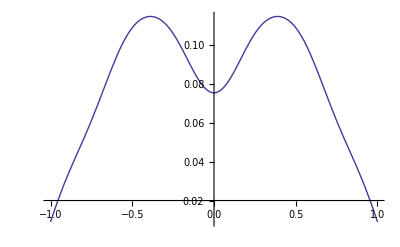

```mathematica
Plot[Φinteraction,{x,-1,1},PlotRange->All]
```

### Generating source code

```mathematica
CForm[Φ]
```

(-400*x*Power(Cos((Pi*x)/2.),2)*Power(Cos(0.5 + Power(x,2) + y),2)*
      Power(Sin((Pi*y)/2.),2) + 8*Power(Cos((Pi*y)/2.),4)*
      Sin(0.5 + Power(x,2) + y) + 
     Pi*Cos(0.5 + Power(x,2) + y)*
      (3 + 4*Cos(Pi*y) + Cos(2*Pi*y) + 100*x*Sin(0.5 + Power(x,2) + y) + 
        100*x*Cos(Pi*x)*Sin(0.5 + Power(x,2) + y))*Tan((Pi*y)/2.))/
   (50.*Power(Pi,2))

```mathematica
Chop[Φinteraction]//CForm
```

(2*Sin((5.353981633974483 - 5*Power(x,2) + 
         0.3183098861837907*x*(1. + Cos(Pi*x))*Sin(Pi*x)*
          (5.38960988787839*Cos(1.*Power(x,2)) - 
            18.853993307917676*Sin(1.*Power(x,2))) - 
         0.10132118364233778*Power(1. + Cos(Pi*x),2)*
          ((5.38960988787839 - 37.70798661583535*Power(x,2))*Cos(1.*Power(x,2)) + 
            (-18.853993307917676 - 10.77921977575678*Power(x,2))*Sin(1.*Power(x,2))
            ))/5.))/(5.*Pi)

## Solving for α required to satisfy the given shear stress distribution

This is not used.  Instead, the above source term is added to the interaction law.

```mathematica
soln=NSolve[ Γ[0]/b (D[τ̃,y]/.y->0) + Γ[x] Γp[x]/a^2 D[φ[τ̃],x]+Γ[x]^2/a^2 D[φ[τ̃],{x,2}]==D[fhat[x,αp,R],{x,2}],αp]
```

{{αp→-(2. (-0.127324 Cos[0.5+x^2]+0.063662 (1.+Cos[3.14159 x]) Sin[3.14159 x] ((5.38961-1.77636×10^-15 ⅈ) x Cos[(1.+0. ⅈ) x^2]-(18.854+4.44089×10^-16 ⅈ) x Sin[(1.+0. ⅈ) x^2])-0.0202642 (1.+Cos[π x])^2 ((9.427+2.22045×10^-16 ⅈ) ((-4.+0. ⅈ) x^2 Cos[(1.+0. ⅈ) x^2]-(2.+0. ⅈ) Sin[(1.+0. ⅈ) x^2])+(2.6948-8.88178×10^-16 ⅈ) ((2.+0. ⅈ) Cos[(1.+0. ⅈ) x^2]-(4.+0. ⅈ) x^2 Sin[(1.+0. ⅈ) x^2]))))/(24.674 Sec[1.5708 x]^2 Tan[1.5708 x]-(1542.13 Sec[1.5708 x]^4 Tan[1.5708 x]^2)/((0.25+25. Tan[1.5708 x]^2)^(3/2))+(61.685 Sec[1.5708 x]^4)/(√(0.25+25. Tan[1.5708 x]^2))+(123.37 Sec[1.5708 x]^2 Tan[1.5708 x]^2)/(√(0.25+25. Tan[1.5708 x]^2)))}}

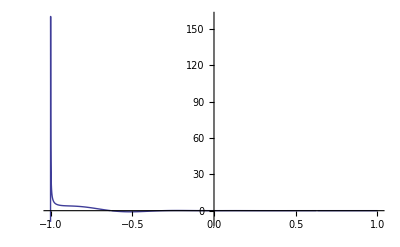

```mathematica
Plot[αp/.soln[[1]],{x,-1,1},PlotRange->All]
```